```mathematica
lst=Table[0,8,31];
```

```mathematica
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-15,0}]~Join~Table[fCtauP[i],{i,1,15}]];
```

General::munfl: Exp[-822.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-767.854] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-713.007] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,8}],DataRange->{-15,15}]]
```

-Graphics-

```mathematica
corr0=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana\\corr_s_0.dat",Number];
corr1=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana\\corr_s_1.dat",Number];
corr2=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana\\corr_s_2.dat",Number];
corr3=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana\\corr_s_3.dat",Number];
corr4=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana\\corr_s_4.dat",Number];
corr5=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana\\corr_s_5.dat",Number];
corr6=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana\\corr_s_6.dat",Number];
corr7=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana\\corr_s_7.dat",Number];
```

```mathematica
plst=Table[0,{i,8},{j,31},{k,2}];
For[i=0,i<8,i++,plst[[i+1]]=Transpose[{Table[i,{i,-15,15}],lst[[i+1]]}]];
```

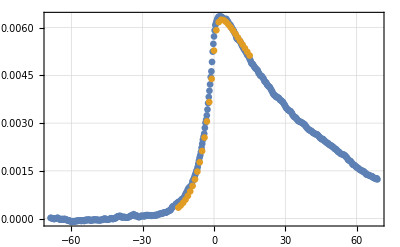

```mathematica
scalF=5.5;
pcr2=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr2}];

ListPlot[{pcr2,plst[[3]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed"]
```

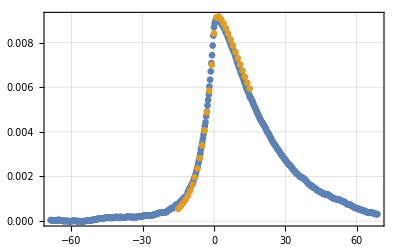

```mathematica
scalF=5.5;
pcr4=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr4}];

ListPlot[{pcr4,plst[[5]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed"]
```

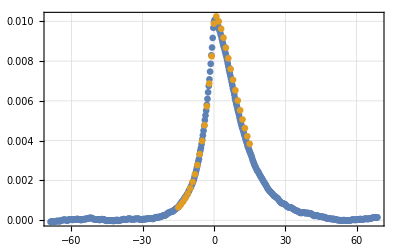

```mathematica
scalF=5.5;
pcr6=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr6}];

ListPlot[{pcr6,plst[[7]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed"]
```

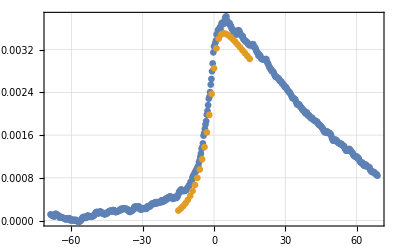

```mathematica
scalF=5.5;
pcr1=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr1}];

ListPlot[{pcr1,plst[[2]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed"]
```

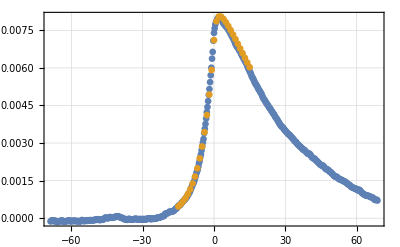

```mathematica
scalF=5.5;
pcr3=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr3}];

ListPlot[{pcr3,plst[[4]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed"]
```

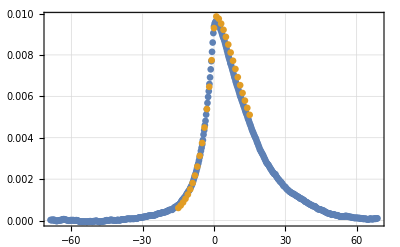

```mathematica
scalF=5.5;
pcr5=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr5}];

ListPlot[{pcr5,plst[[6]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed"]
```

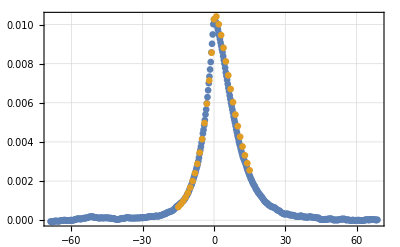

```mathematica
scalF=5.5;
pcr7=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr7}];

ListPlot[{pcr7,plst[[8]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All]
```

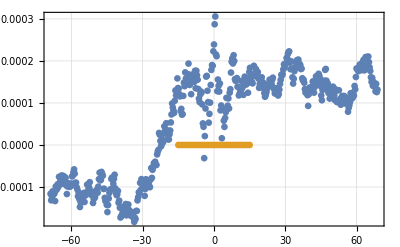

```mathematica
scalF=5.5;
pcr0=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr0}];

ListPlot[{pcr0,plst[[1]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed"]
```